```mathematica
Dens[en_]=FourierTransform[2*(BesselJ[0,t/2])^2/Sqrt[2Pi],t,en,Assumptions->en>-1&&en<1]
```

(4 EllipticK[1-en^2])/π^2

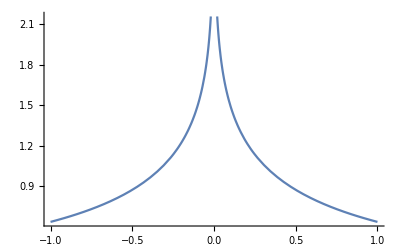

```mathematica
Plot[Dens[x],{x,-1,1}]
```

```mathematica
Denstab={N@#,N@Dens[#]}&/@Table[i/1000,{i,-1000,1000}]
```

{{-1.,0.63662},{-0.999,0.636938},{-0.998,0.637257},{-0.997,0.637576},{-0.996,0.637896},{-0.995,0.638216},{-0.994,0.638537},{-0.993,0.638858},{-0.992,0.639179},{-0.991,0.639501},1981,{0.991,0.639501},{0.992,0.639179},{0.993,0.638858},{0.994,0.638537},{0.995,0.638216},{0.996,0.637896},{0.997,0.637576},{0.998,0.637257},{0.999,0.636938},{1.,0.63662}}
 |  |  |  |

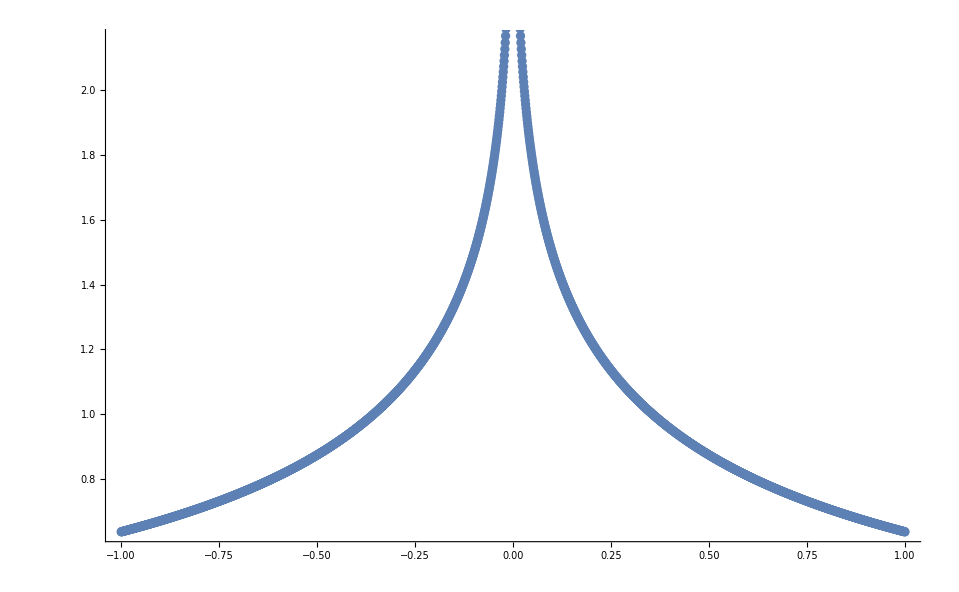

```mathematica
Show[{Plot[Dens[x],{x,-1,1}],ListPlot[Denstab]}]
```

```mathematica
Export["dens2d.dat",Denstab]
```

dens2d.dat

```mathematica
ekin[beta_]:=NIntegrate[Dens[x]*x/(Exp[x*beta]+1),{x,-1,1}]
```

```mathematica
betatab={26.0,27.0,28.0,29.0,30.0,31.0,32.0,33.0,34.0,35.0,40.0,60.0,80.0}
```

{26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,40.,60.,80.}

```mathematica
ekintab={#,ekin[#]}&/@betatab
```

{{26.,-0.401237},{27.,-0.401497},{28.,-0.401732},{29.,-0.401945},{30.,-0.402139},{31.,-0.402316},{32.,-0.402478},{33.,-0.402627},{34.,-0.402764},{35.,-0.40289},{40.,-0.403396},{60.,-0.404371},{80.,-0.404741}}

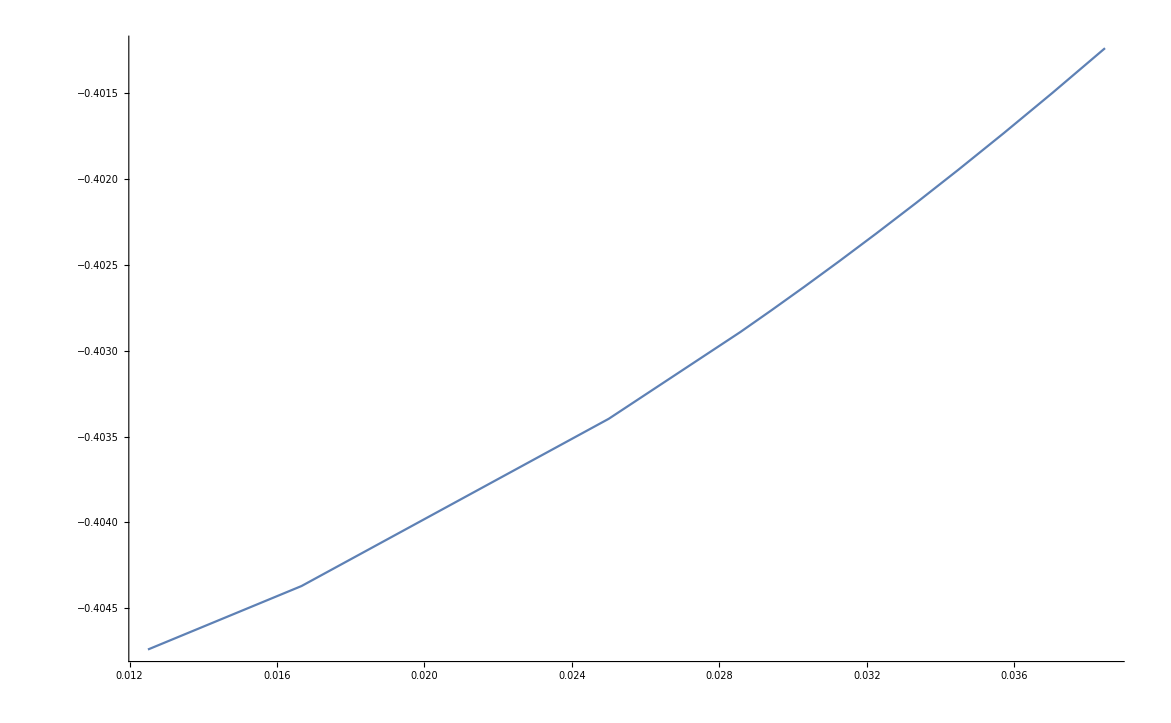

```mathematica
ListPlot[ekintab,Joined->True]
```

```mathematica
Export["EkinU0.dat",ekintab]
```

EkinU0.dat

```mathematica
occup[beta_,en_]=Dens[en]/(Exp[beta*en]+1)
```

(4 EllipticK[1-en^2])/((1+ⅇ^(beta en)) π^2)

```mathematica
occup1[beta_]:=({N@#1,N@occup[beta,#1]}&/@Table[i/10000,{i,-10000,10000}])
```

```mathematica
Export["occup_beta"<>ToString[#]<>"0.dat",occup1[#]]&/@betatab
```

{occup_beta26.0.dat,occup_beta27.0.dat,occup_beta28.0.dat,occup_beta29.0.dat,occup_beta30.0.dat,occup_beta31.0.dat,occup_beta32.0.dat,occup_beta33.0.dat,occup_beta34.0.dat,occup_beta35.0.dat,occup_beta40.0.dat,occup_beta60.0.dat,occup_beta80.0.dat}

```mathematica
Integrate[Dens[x]*x,{x,-1,0}]
```

-4/π^2

```mathematica
beta1tab:=Table[i,{i,26,1000}]
```

```mathematica
ekin1tab:={#,ekin[#]}&/@beta1tab
```

```mathematica
Export["Ekin1U0.dat",ekin1tab]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

Ekin1U0.dat

```mathematica
Integrate[EllipticK[1-x^2]*x,{x,0,1}]
```

1